# 1. Basics (4)

### Problem 1.1

Calculate the following number

11/3 +217/43+29/551-116/23

#### Solution

### Problem 1.2

Calculate the following number:

11./3 +217/43+29/551-116/23

Note the presence of the decimal point in “11.”.

#### Solution

### Problem 1.3

Calculate the exact value of 5^100

#### Solution

### Problem 1.4

Calculate an approximate value of the number given in Problem 1.3.

#### Solution

# 2. Algebra and Trigonometry (9)

### Problem 2.1

Replace x by (2-y) in x^3-x^2+4x

#### Solution

### Problem 2.2

Expand out products and powers in the above result.

#### Solution

### Problem 2.3

Define function f such that f(x)=a x^3 sin(a x).

#### Solution

### Problem 2.4

Use the above-defined function f to evaluate f(√2).

#### Solution

### Problem 2.5

(1) Clear the definition assigned to symbol f in Problem 2.3. (2) Confirm that the definition of f has been cleared by caculating f(√2) again and comparing the result with the answer of Problem 2.4.

#### Solution

### Problem 2.6

Solve the algebraic equation of second order a x^2+b x+c=0.

#### Solution

### Problem 2.7

Find the exact solution(s) to the following algebraic equation:

√(x-1)+√x+√(x+1)=3

#### Solution

### Problem 2.8

The solution to the algebraic equation in Problem 2.7 is real. However, Mathematica cannot simplify the result. Show this by solving the equation numerically.

#### Solution

### Problem 2.9

Transcendental (i.e., non-algebraic) equations cannot be solved with Mathematica commands Solve, NSolve, and Reduce. (1) Confirm this by trying to solve the following transcendental equation: cos(x)=x using these commands. (2) Find the appropriate Mathematica command for solving the equation.

#### Solution

# 3. Plots and Animations (15)

## Simple 2D Plots

### Problem 3.1

Define a function f such that f(x)=e^-x then plot f(x) for x ∈ [0,3].

#### Solution

## List Plots

### Problem 3.2

Define a function f such that f(x)=e^-x then plot f(x) for x ∈ [0,3].

#### Solution

### Problem 3.3

Define a list that contains the following set of data points

{{1,2},{2,4},{3,5},{4,5},{5,4},{6,3},{7,2.5}}

then plot the data points

#### Solution

### Problem 3.4

Plot the list of data points defined in Problem 3.2 as joined points.

#### Solution

## Parametric Plots

### Problem 3.5

A circle can be represented parametrically by

x(ϕ) = sin(ϕ),
y(ϕ) = cos(ϕ)

Use the Mathematica ParametricPlot command to plot this circle for ϕ  ∈ [0, 2π].

#### Solution

### Problem 3.6

Plot parametrically the cycloid defined by

x(ϕ)=sin(ϕ)+1/2 ϕ,
y(ϕ)=cos(ϕ);

for ϕ  ∈ [0, 4π].

#### Solution

## 3D Plots

### Problem 3.7

Plot the following plane wave

A cos((2π)/T t-(2π)/λ x)

for x ∈ [0, 2λ] and t x ∈ [0, 2T]. Hint: Give parameters A, T, and λ numerical values. For instance, let A=T=λ=1.

#### Solution

## Contour Plots

### Problem 3.8

Plot a contour plot of the plane wave of Problem 3.6.

#### Solution

### Problem 3.9

The electric potential at point (x,y) due to a positive, unit charge located at point (x_i,y_i) is given by the following function:

V(x,y)=(8.988×10^9)/(√((x-x)^2+(y-y)^2))

Consider a system of three positive, unit charges forming an equilateral triangle and located at

x_1=0,   y_1=1/(√3),
x_2=-1/2,   y_2=-1/(2 √3),
x_3=1/2,   y_3=-1/(2 √3).

Then, the electric potential due to the system at point (x,y) will be given by

V(x-x_1,y-y_1)+V(x-x_2,y-y_2)+V(x-x_3,y-y_3).

Plot the equipotential lines corresponding to this system of charges for x ∈ [-1, +1] and y ∈ [-1, +1]. 
Hint: Set the number of contour lines to 15.

#### Solution

## 3D Parametric Plots

### Problem 3.10

Curves in 3D space can be represented with the help of one parameter. Plot a 3D parametric plot of the following helix parameterized by u. Let u ∈ [0,20].

x(u) = sin(u);
y(u) = cos(u);
z(u) = u/10;

#### Solution

### Problem 3.11

Surfaces in 3D space can be represented with the help of two parameters. Plot a 3D parametric plot of the following torus parameterized by u and v. Let u ∈ [0,2π] and v ∈ [0,2π].

R = 3;   r = 1.5;
x(u,v) = (R + r cos(v)) sin(u);
y(u,v) = (R + r cos(v)) cos(u);
z(u,v) = r sin(v);

R is the distance from the origin of coordinates to the center of the torus. r is the distance from the center of the torus to its surface. You can use the following values R = 3,   r = 1.

#### Solution

## Animations

### Problem 3.12

Use the Manipulate command to generate a plot of the following harmonic functions and their sum that can be controlled through the value of the phase ϕ_0

Q_1(t)=sin(2π  t)
Q_2(t,ϕ_0)=sin(2π  t+ϕ_0)

Hint: Let ϕ_0 ∈ [-π, π] and t ∈ [0, 3].

#### Solution

### Problem 3.13

Use the Manipulate command to generate a plot of the torus given in Problem 3.11 that can be controlled through the values of R and r.

#### Solution

### Problem 3.14

Use the Animate command to generate an animation of the plot of the following two Gaussian pulses and their sum

G_1(x,t)=ⅇ^(-(x+6-t)^2),
G_2(x,t)=1/2 ⅇ^(-(x+6-t)^2).

Hint: Let the control parameter be t ∈ [0,10] and let x ∈ [-4,4].

#### Solution

### Problem 3.15

Use the Animate command to generate an animation of the plot of the following surface

S(x,y,t) = Cos(x + y - t).

Let the control parameter be t.

#### Solution

# 4. Series (4)

### Problem 4.1

Use Mathematica to test the convergence of the following series.

∑_(n=0)^∞ 1/2^n,
∑_(n=0)^∞ (1+n)/2^(a n),
∑_(n=0)^∞ (sin(n))/2^n,
∑_(n=1)^∞ (-1)^n/n,
∑_(n=1)^∞ ((1+i)/(2-i))^n,
∑_(n=1)^∞ (1+ⅈ)^n,
∑_(n=1)^∞ (Log[n]Sin[n])/2^n

Hint: Try to perform a direct compuation of the sum.

#### Solution

### Problem 4.2

In Problem 4.1, Mathematica was unable to calculate the exact sum of the last series, i.e., ∑_(n=1)^∞ (Log[n]Sin[n])/2^n. Mathematica can do it numerically, though. Calculate this sum numerically.

#### Solution

### Problem 4.3

Expand the following funtions as Mclaurin power series (i.e., Taylor series about the origin) to order 10. Compare your results for the first 5 funtions with eqs. 13.1, 13.2, 13.3, 13.4, 13.5 in the textbook.

sin(x),
cos(x),
e^x,
ln(1+x),
(1+x)^p, 
(e^(-x^2))/(√(1+x^2))sin(5x)

#### Solution

### Problem 4.4

Consider the following function

f(x) = ArcTan(x).

(1) Define the following Taylor series expansions of f(x)

T1(x) = Taylor series expansion at x=0 to 1st order
T3(x) = Taylor series expansion at x=0 to 3rd order
T5(x) = Taylor series expansion at x=0 to 5th order
T7(x) = Taylor series expansion at x=0 to 7th order

Show in a single plot the graphs of f(x), T1(x), T3(x), T5(x), T7(x). Let x ∈ [0,5] and the plot range [0,2]. Observe how the Taylor expansions T1(x), T3(x), T5(x), T7(x) have a range of convergence |x|<1. Outside this range, the expansions do not provide an approximation to f(x), whatever the order

(2) Define the following large-x Taylor series expansions of f(x)

A1(x) = large-x Taylor series expansion to 1st order
A3(x) = large-x Taylor series expansion to 3rd order
A5(x) = large-x Taylor series expansion to 5th order
A7(x) = large-x Taylor series expansion to 7th order

Show in a single plot the graphs of f(x), A1(x), A3(x), A5(x), A7(x). Let x ∈ [0,5] and the plot range [0,2]. Observe how the large-x Taylor expansions A1(x), A3(x), A5(x), A7(x) have a range of convergence |x|>1. Outside this range, the expansions do not provide an approximation to f(x), whatever the order.
Hint: (1) Use the Mathematica command Normal to convert the outputs of the Series command into expressions that Mathematica can plot. (2) Choose a plot style that distinguished between the curves. Eg., you can use PlotStyle→{Thick,Dashed,Dashed,Dashed,Dashed}. (3) Large-x Taylor series expansions are sometimes called expansions at infinity.

#### Solution

### Problem 4.4

Taylor series expansions can be generalized for functions of many variables. Consider the following function:

f(x,y) = sin(x+y)

(1) Find the Taylor series expansion of f at x=0 to 3rd order. 
(2) Find the Taylor series expansion of f at x=0=y to 3rd order.

#### Solution

# 5. Complex Numbers (4)

### Problem 5.1

Using Mathematica, find the real and imaginary parts of the following complex numbers:

(2-i)(3+2i),
(1+2 i)/(3-4i)+(2-i)/(5i),
(1/((1-i)(2-i)(3-i)))^(1/3),
((1+i √3)/(√3+ i))^217.

#### Solution

### Problem 5.2

Using Mathematica, convert the complex numbers given in Problem 5.1 to polar form (i.e., find the absolute values and the arguments of the numbers).

#### Solution

### Problem 5.3

By default, all symbols in Mathematica are complex. Show this by using the Re and Im commands to calculate the real and imaginary parts of z = u + i  v  .

#### Solution

### Problem 5.4

Take the complex number z = u + i  v defined in Problem 5.3. Show that by using the Mathematica Simplify command and declaring u and v as real quantities with the Assumptions option, Re and Im  give the expected results.

#### Solution

# 6. Systems of Linear Equations (2)

### Problem 6.1

Use the Mathematica command Solve to solve the following system of linear equations:

a-3b+c==0
a+b+2c==-1
2a+b-c==2

#### Solution

### Problem 6.2

Use the Mathematica command LinearSolve to solve the same system of linear equations given in Problem 6.1 in matrix form. Compare the result with the solution of Problem 6.1.

#### Solution

# 7. Vectors and Matrices (19)

## Vector Calculations

### Problem 7.1

Calculate the scalar product of the following two vectors

aVec = {a1, a2, a3};
bVec = {b1, b2, b3};

#### Solution

### Problem 7.2

Using the appropriate Mathematica command, calculate (1) the exact value and (2) the numerical value of the angle between the following pairs of vectors:

{1, 0} and {1, 1};
{1/2, (-5 √2)/3,6} and {-1, +1,10}

#### Solution

### Problem 7.3

Calculate the vector cross product of the vectors given in Problem 7.1.

#### Solution

### Problem 7.4

Using the vectors defined in Problem 7.1, check that the scalar product is symmetric and the vector cross product is antisymmetric. Hint: The product * of A and B is symmetric when A*B=B*A; It is antisymmetric when A*B=-B*A.

#### Solution

### Problem 7.5

Show that when A is a vector, Mathematica distinguishes between √(A·A) and √(A^2).

#### Solution

### Problem 7.6

The mixed vector product is a dot product of a vector and a cross product of two other vectors such as A·(B×C). Check that the mixed vector product is invariant with respect to the cyclic permutations of the three vectors, that is, A·(B×C)=C·(A×B)=B·(C×A). Hint: Define 3 vectors (see Problem 7.1) and use the Simplify command to ensure that the answer is in its simplest form.

#### Solution

### Problem 7.7

Check the double cross product identity, that is

A×(B×C)≡B(A·C)-C(A·B)

#### Solution

### Problem 7.8

The Table command can be used to authomatically generate the components of a vector. Use Mathematica to find the 7th component of the following vector

tab=Table[i^2,{i,5,15}].

#### Solution

## Vector Plots

### Problem 7.9

Vector functions of scalar arguments can be plotted with the Mathematica commands VectorPlot, StreamPlot (in 2D) VectorPlot3D (in 3D), as well as with other commands. Using VectorPlot and StreamPlot plot the normalized electric field of a unit, positive charge given by

4π ϵ_0 E(r)=r/r^3

in the x-y plane (z = 0) where x ∈ [-1,+1] and y ∈ [-1,+1]. Hint: (1) since we are interesting only in the field in the x-y plane, we can ignore its z-component and plot only its x- and y-components which leaves us with a 2D function. (2) With VectorPlot you can use 9 for the VectorPoints option; with StreamPlot you can use 100 for the StreamPoints option.

#### Solution

### Problem 7.10

Repeat Problem 7.9 for the following field:

vecField={-x^2+y-1,x-y^2+1}

where x ∈ [-3,+3] and y ∈ [-3,+3]

Hint: You can use 10 for the VectorPoints option and 100 for the StreamPoints option.

#### Solution

### Problem 7.11

Plot the 3D vector plot of the normalized electric field created by two charges with unit magnitude and opposite signs. Let the positive charge be at point (1,1,1) and the negative charge be at point (-1,-1,-1). Hint: You can use 9 for the VectorPoints option and 0.3 for the VectorScale option.

#### Solution

## Matrix Calculations

### Problem 7.12

Use Mathematica to extract (1) the first row (2) the 2nd column, and (3) entry m1_34 of the following matrix:

m1=(1 | 1 | 0 | -1
-2 | 0 | 3 | 0
1 | 2 | -3 | 2
2 | 1 | 0 | -2);

#### Solution

### Problem 7.13

(1) Multiply the following two matrices:

m1=(1 | 1 | 0 | -1
-2 | 0 | 3 | 0
1 | 2 | -3 | 2
2 | 1 | 0 | -2);
m2=(2 | -5 | -1 | 2
0 | 3 | -2 | 3
3 | -2 | 1 | 0
1 | 1 | 1 | 1);

(2) Output the result in matrix form.

#### Solution

### Problem 7.14

Using the two matrices in Problem 7.13, confirm that

detAB = detBA = detA detB

#### Solution

### Problem 7.15

Confirm that

(ABC)^-1=C^-1 B^-1 A^-1

where A, B , and C are complex 3 x 3 matrices.

#### Solution

## Eigenvalues and Eigenvectors

### Problem 7.16

Calculate the eigenvalues and eigenvectors for the the following matrix:

A=(a | b
b | -a).

#### Solution

### Problem 7.17

Use the command Eigensystem to see which eigenvector corresponds to which eigenvalue in Problem 7.16.

#### Solution

### Problem 7.18

(1) Use the Mathematica command HermitianMatrixQ to confirm that the following matrix is Hermitian:

B=(Re[a] | b
Conjugate[b] | Re[a])

(2) Show that the eigenvalues of B are real, while its eigenvectors are generally complex.

Caution: Mathematica sometimes is unable to combine square roots!

#### Solution

### Problem 7.19

A workaround the issue that Mathematica sometimes faces with combining square roots was given by James M. Feagin in “Quantum Methods with Mathematica”, Springer, 1994. A new user-defined command is introduced as follows:

```mathematica
PowerContract[expr_]:=expr//.{m_^q_ n_^q_:>(m n)^q/;!IntegerQ[m]&&!IntegerQ[n],m_^q_ n_^p_:>(m/n)^q/;q≥0&&p==-q&&!IntegerQ[m]&&!IntegerQ[n]};
```

Use this new command in conjunction with FullSimply to persuade Mathematica to output the expected result in part (2) of Problem 7.18.

#### Solution

# 8. Derivatives (3)

### Problem 8.1

Let f(x) = x^a. Caclculate the 1st and 2nd order derivative of f using the the following Mathematica commands:

(1) the D command
(1) the ∂ command
(1) the prime command

#### Solution

### Problem 8.2

Caclculate the 10th order derivative of the function f given in Problem 8.1 using the the general Mathematica command Derivative[Order][Function][Argument].

#### Solution

### Problem 8.3

Solve the following ordinary differential equation:

y''(x) - y’(x)+y(x)=0,
y'(0) = 0 (boundary condition).

#### Solution

# 9. Gradient, Divergence, Curl, and Laplacian (6)

## Gradient

### Problem 9.1

Calculate the gradient of the following scalar field in (1) Cartesian coordinates and (2) cylindrical coordinates:

U(x,y)=x^2+y^2+z^2.

Hint: To calculate the gradient in cylindrical coordinates you can use the replacement command /. to substitute x and y with their cylindrical expressions. Also, use  Simplify to see the results in their simplest form.

#### Solution

## Divergence

### Problem 9.2

Calculate the divergence of the following vector field in (1) Cartesian coordinates and (2) cylindrical coordinates:

V(x,y)=y x^2 i+y j+ x z k.

Hint: See the hint in Problem 8.1.

#### Solution

## Curl

### Problem 9.3

Calculate the curl of the vector field given in Problem 8.2 in (1) Cartesian coordinates and (2) cylindrical coordinates:

Hint: See the hint in Problem 8.1.

#### Solution

## Laplacian

### Problem 9.4

Calculate the Laplacian of the scalar field given in Problem 8.1 in (1) Cartesian coordinates and (2) cylindrical coordinates:

Hint: See the hint in Problem 8.1.

#### Solution

## Identities

### Problem 9.5

Check the following identities:

(1) ∇(ϕ ψ)=ϕ∇ψ+ψ∇ϕ
(2)∇·(ϕ A)=ϕ∇·A+∇ϕ·A
(3)∇·(A×B)=(∇×A)·B-A·(∇×B)

Hint: Use the Simplify command.

#### Solution

## Physical Example: Electric Equipotentials and Field Lines

### Problem 9.6

Consider the normalized electric potential created by a charge +1 located at (1,0,0) and a charge -1 located at (-1,0,0).
(1) Plot the equipotential lines for x ∈ [-3,3] and y ∈ [-3,3]. Hint: Use ContourPlot with 20 Contours.
(2) Calculate the electric field due to this potential.
(3) Plot the streamlines of the electric field for x ∈ [-2,3] and y ∈ [-2.5,2.5]. Hint: Use StreamPlot with 20 VectorPoints.
(4) Combine the two plots of part (1) and (3) and observe how the equipotential lines and the field lines are perpendicular.

#### Solution

# 10. Indefinite, Definite, Multiple, and Line Integrals (8)

## Indefinite Integrals

### Problem 10.1

Calculate the following indefinite integrals:

I1=∫x^a dx
I2=∫cos x dx
I3=∫(1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2))dx

#### Solution

## Definite Integrals

### Problem 10.2

Calculate (1) the exact and (2) the numerical values of the following definite integrals:

I1=∫_1^2 x^3 dx
I2=∫_1^2 cos x dx
I3=∫_1^2 (1-2x+3 x^2)/(x(1+x^2)(1+x+2 x^2))dx

#### Solution

## Multiple Integrals

### Problem 10.3

Calculate the following indefinite integral:

∫∫z(x^2+y^2) sin x cos y dx dy dz

#### Solution

### Problem 10.4

(1) Calculate the area of a rectangle x ∈ [-a/2,a/2] and y ∈ [-b/2,b/2] . 
(2) Show that the result is independent of the integration order.

#### Solution

### Problem 10.5

Caculate the area of the circle of center (0,0) and radius R 
(1) in Cartesian coordinates
(2) in polar coordinates

#### Solution

### Problem 10.6

The ellipsoid is a generalization of the sphere. An ellipsoid of center (0,0,0) and semi-major axes a, b, c is defined by the following equation:

x^2/a^2+y^2/b^2+z^2/c^2=1

(1) Caculate the volume of this ellipsoid.
(2) Show that the formula gives the volume of a sphere when a=b=c. Hint: Use the replacement command “/.”.
(3) Plot the ellipsoid for a=4, b=2.5, c=1. Hint: Use the Ellipsoid command.

#### Solution

### Problem 10.7

Calculate the volume of the torus (see Problem 3.11) 
(1) using the Assumptions option to indicate that R>0 and r>0.  
(2) without using the Assumptions option to indicate that R>0 and r>0.
(3) In which case is the computation faster? 
Hint: (1) Cylindrical coordinates are convenient to calculate the volume of the torus, because it has rotational symmetry. (2) You can use the AbsoluteTiming command to display how much time it takes Mathematica to perform the computation

#### Solution

## Line Integrals

### Problem 10.8

Calculate the perimenter of the ellipse defined by the following equation:

x^2/a^2+y^2/b^2=1

#### Solution

# 11. Fourier Series and Transforms (3)

### Problem 11.1

Compute the 3rd order Fourier series expansion of the following functions

(1)|t| 
(2)t^2
(3)ⅇ^-t

Plot each function superimposed on its Fourier series expansion

#### Solution

### Problem 11.2

Find the 3rd coefficient in the Fourier series expansions of the following functions given in Problem 11.1.

#### Solution

### Problem 11.3

Compute the Fourier transforms of the following functions

(1)e^(-t^2)sin t
(2) 1/(1+t^2)
(3)1

#### Solution

# 12. Analytic Functions, Contour Integrals, and Residue Theorem (5)

### Problem 12.1

Find the residues of the following functions at the specified points 
(sin π z)/(4 z^2-1) at z=1/2
1/(z^2-5z+6) at z=2
z^3/(sin (z-2)) at z=2

Note that the the ordinary Riemann definite integrals are divergent.

#### Solution

### Problem 12.2

Find the Cauchy principal values of the following integrals
∫_-1^2 1/x ⅆx
∫_1^4 1/(x-2)^5 ⅆx
∫_0^π tan xⅆx

Note that the the ordinary Riemann definite integrals are divergent.

#### Solution

### Problem 12.3

Use the commands ContourPlot and Plot3D to visualize the branch cuts of the following functions

(1) √z
(2) ln(z)

Hint:Define z=x+iy then plot the real and imaginary parts of the functions. You can set x ∈ [-10,10] and  y ∈ [-10,10]

#### Solution

### Problem 12.4

Calculate the following contour integral

int1=∮_(|z|=2)  (1−e^z+z)/((z^3(z-1))^2)

(1) by using the Cauchy integral theorem
(2) by parametrizing z over the given circle

#### Solution

### Problem 12.5

The goal of the following problem is to reproduce Figure 10.5 of the textbook (Example 5, Section 10, Chapter 14).
The below plots show (1) equipotentials (solid lines) and (2) field lines (dashed lines) at the end of a semi-infinite capacitor.
The plates of the capacitor are at y = π and y = -π and extend over the range x ∈ (- ∞, -1].
The plots show only the y > 0 equipotentials and field lines.
Modify the given codes so that the plots show equipotentials and field lines for both y > 0 and y < 0.

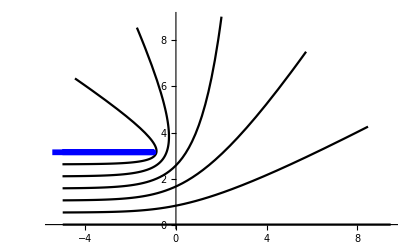

```mathematica
potplot1=ParametricPlot[{{u+Exp[u],0},{u+Exp[u]Cos[Pi/6],Pi/6+Exp[u]Sin[Pi/6]},{u+Exp[u]Cos[Pi/3],Pi/3+Exp[u]Sin[Pi/3]},{u+Exp[u]Cos[Pi/2],Pi/2+Exp[u]Sin[Pi/2]},{u+Exp[u]Cos[2Pi/3],2Pi/3+Exp[u]Sin[2Pi/3]},{u+Exp[u]Cos[5Pi/6],5Pi/6+Exp[u]Sin[5Pi/6]},{u+Exp[u]Cos[Pi],Pi+Exp[u]Sin[Pi]}},{u,-5,2.01},PlotStyle->{Black,Black,Black,Black,Black,Black,{Blue,Thickness[0.01]}}]
```

Similarly, the electric field lines

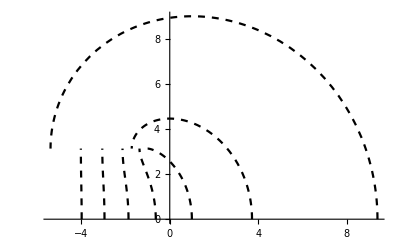

```mathematica
eplot1=ParametricPlot[{{-4+Exp[-4]Cos[v],v+Exp[-4]Sin[v]},{-3+Exp[-3]Cos[v],v+Exp[-3]Sin[v]},{-2+Exp[-2]Cos[v],v+Exp[-2]Sin[v]},{-1+Exp[-1]Cos[v],v+Exp[-1]Sin[v]},{0+Exp[0]Cos[v],v+Exp[0]Sin[v]},{1+Exp[1]Cos[v],v+Exp[1]Sin[v]},{2+Exp[2]Cos[v],v+Exp[2]Sin[v]}},{v,0,Pi},PlotStyle->{{Black,Dashed}}]
```

Equipotentials and field lines combined (showing they are always perpendicular to each other).

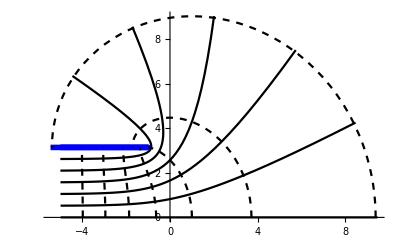

```mathematica
Show[potplot1,eplot1]
```

#### Solution

# 13. Legendre and Associated Legendre Polynomials (2)

### Problem 13.1

Here is Legendre’s equation

(1 - x^2) y'' - 2 x y'+ n (n + 1) y= 0

Mathematica recognizes it as being solved by Legendre polynomials (LegendreP[n,x]) and the Legendre functions of the 2nd kind (LegendreQ[n,x])

```mathematica
DSolve[(1-x^2)y''[x]-2x y'[x] + n(n+1)y[x]==0,y[x],x]
```

{{y[x]→C[1] LegendreP[n,x]+C[2] LegendreQ[n,x]}}

Calculate and plot
(1) the first 5 Legendre polynomials
(2) the first 5 Legendre functions of the 2nd kind

#### Solution

### Problem 13.2

Here is the associated Legendre equation

(1 - x^2) y'' - 2 x y'+ (n (n + 1)- m^2/(1-x^2)) y= 0

Mathematica recognizes it as being solved by the associated Legendre polynomials (LegendreP[n,m,x]) and the Legendre functions of the 2nd kind (LegendreQ[n,m,x])

```mathematica
DSolve[(1-x^2)y''[x]-2x y'[x] + (n(n+1)-m^2/(1-x^2))y[x]==0,y[x],x]
```

{{y[x]→C[1] LegendreP[n,m,x]+C[2] LegendreQ[n,m,x]}}

Calculate and plot
(1) the associated Legendre polynomials for n=1
(2) the associated Legendre functions of the 2nd kind for n=1

#### Solution

# 14. Bessel’s Functions (3)

### Problem 14.1

Here is Bessel’s equation

x^2 y'' +  x y'+ (x^2-p^2) y= 0

Mathematica recognizes it as being solved by Bessel’s functions of the 1st kind (BesselJ[p,x]) and Bessel’s functions of the 2nd kind (BesselY[p,x])

```mathematica
DSolve[x^2 y''[x]+x y'[x] + (x^2-p^2)y[x]==0,y[x],x]
```

{{y[x]→BesselJ[p,x] C[1]+BesselY[p,x] C[2]}}

Calculate and plot
(1) the first 4 Bessel functions of the 1st kind
(2) the first 4 Bessel functions of the 2nd kind

#### Solution

### Problem 14.2

Find the the 2nd zero of J_0 and the 1st zero of Y_3

#### Solution

### Problem 14.3

Use Mathematica to determine the behavior of J_p(x) to zeroth order for large arguments and for small arguments. Hint: Use the Series command.

#### Solution

# 15. The Heat Equation (1)

### Problem 15.1

(1) Use the NDSolve command to solve numerically the heat equation in 1D assuming that: 
(i) the initial state of the temperature field at t=0 is given by T(x,0)=sin((5π x)/L),  where x ∈ [0,L].
(ii) the boundary conditions are given by T(0,t)=0 and  T(L,t)=0.
(iii) the thermal diffusivity κ=0.03.
(2) Plot the solution T(x,t). 
Hint: (1) Let t ∈ [0,1] and L=1. (2) To plot the solution, use the solution as a rule and substitute it into T(x,t). Afterwards, use the Evaluate command to turn the result into a function that can plotted.

#### Solution

# 16. Wave Equation (1)

### Problem 16.1

Repeat Problem 15.1 for the wave equation in 1D assuming that: 
(i) the propagation velocity is 1 
(ii) the initial conditions are given by u(x,0)=Sin(x) and  (∂u(x,t))/(∂t)|_(t=0)=0.
(ii) the boundary conditions are given by u(0,t)=t sin(t) and  u(2π,t)=0.
Hint: Let t ∈ [0,10].

#### Solution

# 17. Integral Transform Solutions of PDEs (2)

### Problem 17.1

(1) Solve the following differential equation using the Laplace transform:

y''(t) + y(t) = sin(t)

(2) Compare the solution with the solution found directly using the DSolve command.

#### Solution

### Problem 17.2

(1) Solve the following differential equation using the Fourier transform:

y''(t) + y(t) = sin(t)

(2) Compare the solution with the solutions found directly using the DSolve command and the solution found using the Laplace transform in Problem 17.1 .

#### Solution